## settings

### functions

```mathematica
getVarianteTwoArg=RandomVariate@MultinomialDistribution[#1,ConstantArray[1/#2,#2]]&;
```

### initial parameters

```mathematica
numberOfContainers=8; (*количество контейнеров*)
numberOfVehicles=2;(*количество машин*)
numberOfStacks=4;(*количество стеков*)
```

```mathematica
ϵ=0.1;
shareOfPairsBlocks=0.05;
```

## generate initial data

```mathematica
vertices1=Range@numberOfContainers;(*множество вершин V1*)
vertices2=vertices1+numberOfContainers;(*множество вершин V2*)
```

```mathematica
{pointsVertices1,pointsVertices2}=Table[RandomReal[{1,5},{numberOfContainers,2}],2];(*начальное и конечное положение контейнеров, случайные позиции на плоскости*)
distanceMatrix=DistanceMatrix[pointsVertices1,pointsVertices2];(*временные затраты на перемещение между слоями*)
```

```mathematica
δ1=δ2=Ceiling@Mean@Flatten@distanceMatrix;
```

```mathematica
outArcs=MapThread[DirectedEdge,{vertices1,vertices2}] ;(*исходящие вершины первого слоя*)
inArcs=DeleteCases[Flatten[Outer[DirectedEdge,vertices2,vertices1]],i_->j_/;i-numberOfContainers==j];(*входящие вершины первого слоя*)
startArcs=Thread[DirectedEdge[0,vertices1]];(*выезд из 0 вершины*)
endArcs=Thread[DirectedEdge[vertices2,2numberOfContainers+1]] ;(*въезд в вершину 2n+1*)
arcs=Join[startArcs,inArcs,outArcs,endArcs];(*множество всех дуг в графе*)
```

```mathematica
stacks=TakeList[RandomSample@vertices1,getVarianteTwoArg[numberOfContainers,numberOfStacks]];(*разбитие вершин на стеки*)
```

```mathematica
{pairsVertices1,pairsVertices2}=RandomSample[#,Floor[shareOfPairsBlocks Length@#]]&@Subsets[#,{2}]&/@{vertices1,vertices2}; (*множества PV1,PV2*)
```

```mathematica
K=numberOfVehicles(Total[Max/@distanceMatrix]+Total[Max/@distanceMatrixᵀ]);
```

#### Переменные

```mathematica
varsX2=Flatten[x[#[[1]],#[[2]]]&/@Join[inArcs,outArcs]];
varsX3=Sort[Flatten[Table[Sort[x[#[[1]],#[[2]],k]&/@Join[startArcs,endArcs]],{k,numberOfVehicles}]]];
varsX=Join[varsX2,varsX3];
```

```mathematica
varsU1=u[#]&/@Join[vertices1,vertices2];
lstu2=u[#]&/@{0,2*numberOfContainers+1};
varsU2=Sort[Table[Append[lstu2[[i]],k],{i,Length@lstu2},{k,1,numberOfVehicles}]];
varsU=Join[varsU1,Flatten@varsU2];
```

```mathematica
varsy1=y1[#[[1]],#[[2]]]&/@pairsVertices1;
varsy2=y2[#[[1]],#[[2]]]&/@pairsVertices2;
```

```mathematica
vars=Join[varsX,varsU,varsy1,varsy2,{umax}];
```

#### Критериии оптимизации

```mathematica
objFun1=Total[Last@varsU2-First@varsU2];
objFun2=umax;
```

```mathematica
weights={0.5,0.5};
objFun=Dot[weights,{objFun1,objFun2}];
c=Last@CoefficientArrays[objFun,vars];
```

#### Ограничения

```mathematica
con1=Table[Total[Cases[varsX2,x[i,_]]],{i,vertices1}];
rhs1=ConstantArray[{1,0},Length@con1];
```

```mathematica
con2=Table[Total[Cases[varsX3,x[0,_,k]]],{k,numberOfVehicles}];
rhs2=ConstantArray[{1,-1},Length@con2];
```

```mathematica
con3=Table[Total[Cases[varsX3,x[0,i,_]]]+Total[Cases[varsX2,x[_,i]]],{i,vertices1}];
rhs3=ConstantArray[{1,0},Length@con3];
```

```mathematica
con4=Table[Total[Cases[varsX3,x[i,2*numberOfContainers+1,_]]]+Total[Cases[varsX2,x[i,_]]],{i,vertices2}];
rhs4=ConstantArray[{1,0},Length@con4];
```

```mathematica
con5=Table[Total[Cases[varsX3,x[0,_,k]]]-Total[Cases[varsX3,x[_,2*numberOfContainers+1,k]]],{k,numberOfVehicles}];
rhs5=ConstantArray[{0,0},Length@con5];
```

```mathematica
con6=umax-Last@varsU2;
rhs6=ConstantArray[{0,1},Length@con6];
```

```mathematica
con7=Flatten@Table[Cases[Flatten@varsU2,u[0,k]]-K*Total[Cases[varsX3,x[0,_,k]]],{k,numberOfVehicles}];
rhs7=ConstantArray[{0,-1},Length@con7];
```

```mathematica
pairsOfPriorInStack=Flatten[Subsets[#,{2}]&/@stacks,1];
con8=Flatten[Cases[varsU1,u[#[[1]]]]-Cases[varsU1,u[#[[2]]]]&/@pairsOfPriorInStack];
rhs8=ConstantArray[{δ1,1},Length@con8];
```

```mathematica
con9=Flatten[-Cases[varsU1,u[#[[1]]]]+Cases[varsU1,u[#[[2]]]]-K*Cases[varsy1,y1[#[[1]],#[[2]]]]&/@pairsVertices1];
rhs9=ConstantArray[{-δ2,-1},Length@con9];
```

```mathematica
con10=Flatten[Cases[varsU1,u[#[[1]]]]-Cases[varsU1,u[#[[2]]]]+Cases[varsy1,y1[#[[1]],#[[2]]]]&/@pairsVertices1];
rhs10=ConstantArray[{K-δ2,-1},Length@con10];
```

```mathematica
con11=Flatten[-Cases[varsU1,u[#[[1]]]]+Cases[varsU1,u[#[[2]]]]-K*Cases[varsy2,y2[#[[1]],#[[2]]]]&/@pairsVertices2];
rhs11=ConstantArray[{-δ2,-1},Length@con11];
```

```mathematica
con12=Flatten[Cases[varsU1,u[#[[1]]]]-Cases[varsU1,u[#[[2]]]]+Cases[varsy2,y2[#[[1]],#[[2]]]]&/@pairsVertices2];
rhs12=ConstantArray[{K-δ2,-1},Length@con12];
```

```mathematica
con13=Flatten[-Cases[varsU1,u[#[[1]]]]+Cases[varsU1,u[#[[2]]]]-K*Cases[varsX2,x[#[[1]],#[[2]]]]&/@Join[inArcs,outArcs]];
rhs13=Which[#[[2]]>numberOfContainers,{distanceMatrix[[#[[1]]]][[#[[2]]-numberOfContainers]]-K,1},#[[1]]>numberOfContainers,{distanceMatrix[[#[[2]]]][[#[[1]]-numberOfContainers]]-K,1}]&/@Join[inArcs,outArcs];
```

```mathematica
con14=Flatten@Table[-Cases[varsU1,u[#[[1]]]]+Cases[Flatten@varsU2,u[2*numberOfContainers+1,k]]-K*Cases[varsX3,x[#[[1]],2*numberOfContainers+1,k]]&/@endArcs,{k,numberOfVehicles}];
rhs14=ConstantArray[{-K,1},Length@con14];
```

```mathematica
con15=Flatten@Table[Cases[varsU1,u[#[[2]]]]-Cases[Flatten@varsU2,u[0,k]]-K*Cases[varsX3,x[0,#[[2]],k]]&/@startArcs,{k,numberOfVehicles}];
rhs15=ConstantArray[{-K,1},Length@con15];
```

### LinearProgramming

```mathematica
lu=Join[ConstantArray[{0,1},Length@varsX],ConstantArray[{0,K},Length@Flatten[varsU]],ConstantArray[{0,1},Length@varsy1],ConstantArray[{0,1},Length@varsy2],{{0,K}}];
domain=Join[ConstantArray[Integers,Length@varsX],ConstantArray[Reals,Length@Flatten[varsU]],ConstantArray[Integers,Length@varsy1],ConstantArray[Integers,Length@varsy2],{Reals}];
matr=Last@CoefficientArrays[Join[con1,con2,con3,con4,con5,con6,con7,con8,con9,con10,con11,con12,con13,con14,con15],vars];
bb=Join[rhs1,rhs2,rhs3,rhs4,rhs5,rhs6,rhs7,rhs8,rhs9,rhs10,rhs11,rhs12,rhs13,rhs14,rhs15];
```

```mathematica
sol=LinearProgramming[c,matr,bb,lu,domain]
```

{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0.,11.1436,11.5484,7.17656,3.,0.,4.83245,7.16776,0.92969,12.6159,13.5586,9.71758,5.34421,3.37338,7.11979,11.419,0.,0.,12.6159,13.5586,1,1,13.5586}

```mathematica
x2=Sort[DeleteCases[sol[[;;Length@varsX2]]*varsX2,0]]
```

{x[1,9],x[2,10],x[3,11],x[4,12],x[5,13],x[6,14],x[7,15],x[8,16],x[9,5],x[12,2],x[13,8],x[14,7],x[15,4],x[16,3]}

```mathematica
x3=DeleteCases[sol[[Length@varsX2+1;;Length@varsX2+Length@varsX3]]*varsX3,0];
GroupBy[x3,Last]
```

<|2→{x[0,1,2],x[11,17,2]},1→{x[0,6,1],x[10,17,1]}|>

```mathematica
vert=Join[{#[[1]],#[[2]]}&/@x2,{#[[1]],#[[2]]}&/@x3];
```

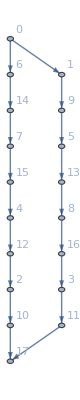

```mathematica
Graph[#[[1]]->#[[2]]&/@vert,VertexLabels->"Name"]
```

### GurobiOptimization

```mathematica
Get[StringJoin[NotebookDirectory[],"\\Gurobi-main\\GurobiOptimization.wl"]];
directory = "C:\\gurobi912\\win64\\bin\\";
```

```mathematica
solGurobi=GurobiOptimization[Normal@c,Normal@matr,bb,lu,domain,directory];
```

```mathematica
solGurobi
```

{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,11.145,11.55,7.178,3.,0,4.833,7.168,0.93,12.618,13.56,9.719,5.344,3.374,7.121,11.42,0,0,13.56,12.618,1,1,13.56}